Operacion de grupo para una curva eliptica

```mathematica
f[x_]:=x^3-43x+166
```

```mathematica
ecurve[r_,s_]:=ContourPlot[y^2==f[x],{x,-r,r},{y,-s,s},Axes->None,Frame->False,ContourStyle->Blue]
```

```mathematica
axis[r_,s_]:=Graphics[{LightGray,Line[{{{-r,0},{r,0}},{{0,-s},{0,s}}}]}]
```

```mathematica
line[x_]:=Line[Table[po[[i]],{i,x}]]
```

```mathematica
po={{3,8},{3,-8},{-5,16},{-5,-16},{11,32},{11,-32}};
```

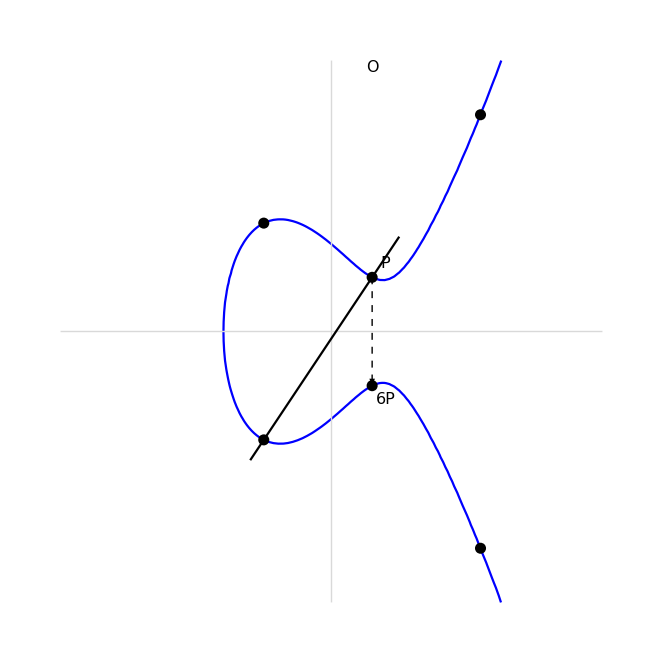

```mathematica
Show[ecurve[20,40],axis[20,40],
Plot[3x-1,{x,-6,5},PlotStyle->{Black}],
Graphics[{Dashed,Arrowheads[{{.03,.55}}],Arrow[{po[[1]],po[[2]]}]}],
Graphics[{PointSize[0.012],Inset[Style["P",Italic,16],{4,10}],Inset[Style["6P",Italic,16],{4,-10}],
Inset[Style["O",Italic,16],{3,39}],
Point[po]}]]
```

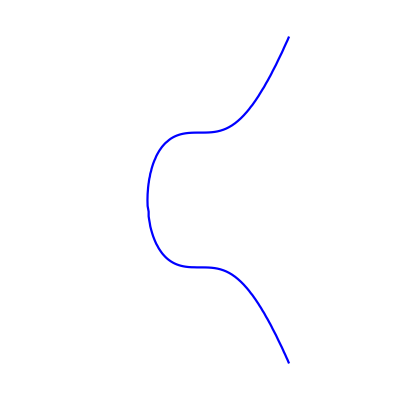

```mathematica
ContourPlot[y^2==x^3+17,{x,-8,8},{y,-10,10},Axes->None,Frame->False,ContourStyle->Blue]
```

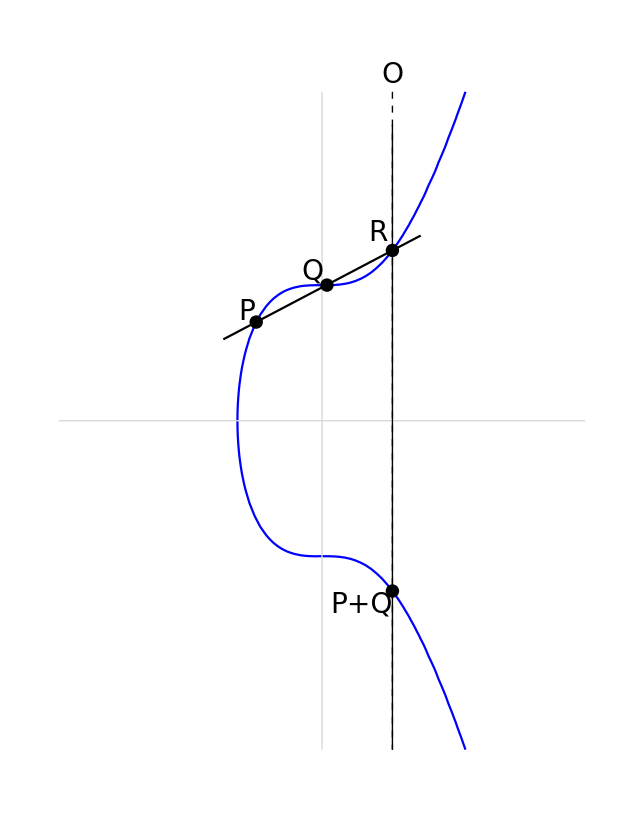

```mathematica
Show[Graphics[Inset[Style["O",Italic,28],{137/64,10.5}]],
ContourPlot[y^2==x^3+17,{x,-3,6},{y,-10,10},Axes->None,Frame->False,ContourStyle->Blue],axis[8,10],
Plot[223/424 x+859/212,{x,-3,3},PlotStyle->{Black}],
Graphics[{Dashed,Line[{{137/64,10},{137/64,-10}}]}],
Graphics[Line[{{137/64,9},{137/64,-10}}]],
Graphics[{PointSize[0.015],Inset[Style["P",Italic,28],{-2.3,3.3}],
Inset[Style["Q",Italic,28],{-0.3,√17+0.4}],
Inset[Style["R",Italic,28],{1.7,5.7}],
Inset[Style["P+Q",28],{1.2,-5.6}],
Point[{{-2,3},{137/64,2651/512},{0.15,√17},{137/64,-2651/512}}]}]]
```

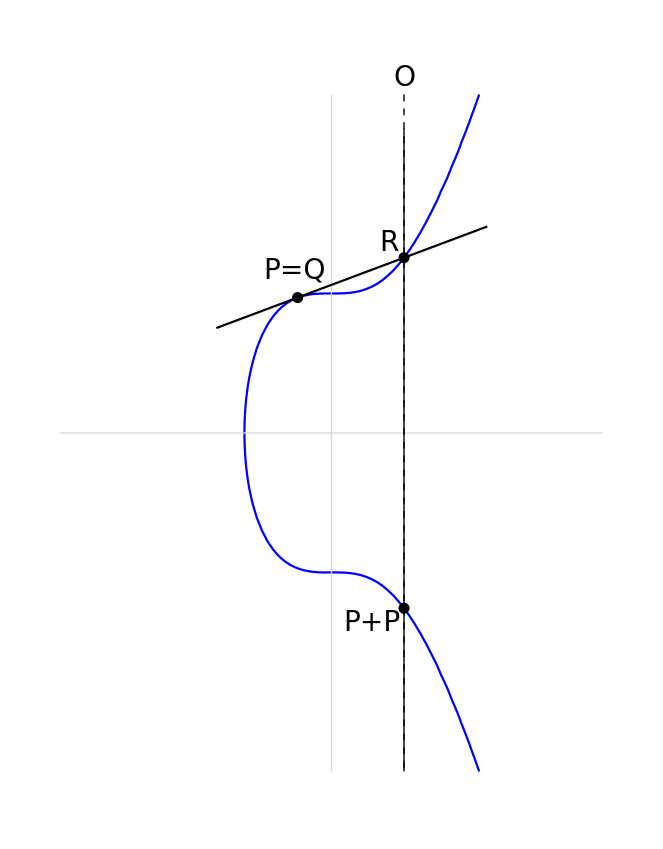

```mathematica
Show[Graphics[Inset[Style["O",Italic,28],{137/64,10.5}]],
ContourPlot[y^2==x^3+17,{x,-3,6},{y,-10,10},Axes->None,Frame->False,ContourStyle->Blue],axis[8,10],
ParametricPlot[{-1,4}+x{-8,-3},{x,-0.7,0.3},PlotStyle->{Black}],
Graphics[{Dashed,Line[{{137/64,10},{137/64,-10}}]}],
Graphics[Line[{{137/64,9},{137/64,-10}}]],
Graphics[{PointSize[0.012],Inset[Style["P=Q",28],{-1.1,4.8}],
Inset[Style["R",Italic,28],{1.7,5.6}],
Inset[Style["P+P",28],{1.2,-5.6}],
Point[{{-1,4},{137/64,2651/512},{137/64,-2651/512}}]}]]
```

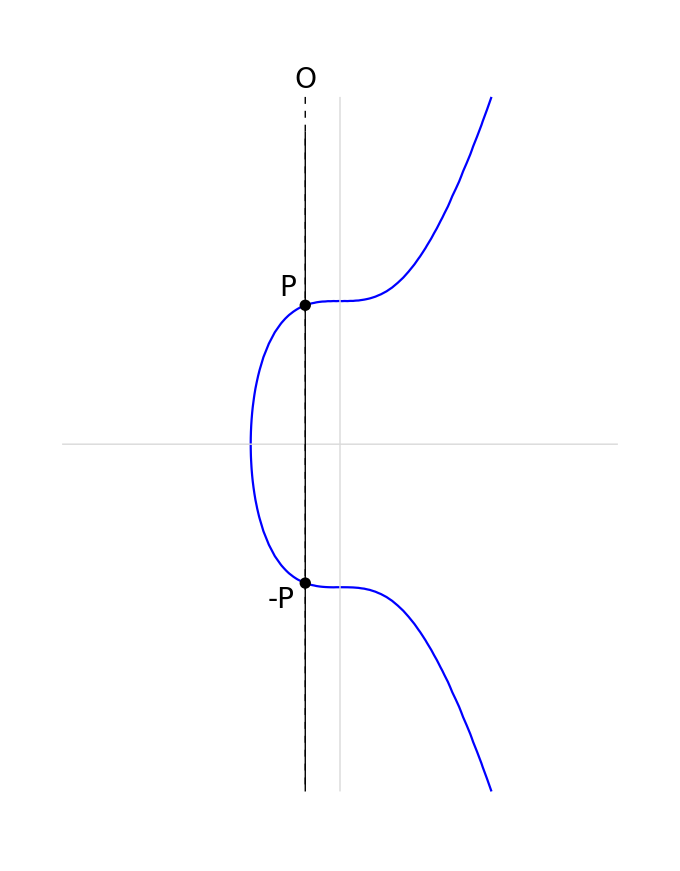

```mathematica
Show[Graphics[Inset[Style["O",Italic,28],{-1,10.5}]],
ContourPlot[y^2==x^3+17,{x,-3,6},{y,-10,10},Axes->None,Frame->False,ContourStyle->Blue],axis[8,10],
Graphics[Line[{{-1,9},{-1,-10}}]],
Graphics[{Dashed,Line[{{-1,10},{-1,-10}}]}],
Graphics[{PointSize[0.012],Inset[Style["P",28],{-1.5,4.5}],
Inset[Style["-P",Italic,28],{-1.7,-4.5}],
Point[{{-1,4},{-1,-4}}]}]]
```